## Rossler System

```mathematica
Clear[a,b,c]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z, x +a y,b+z (x  - c)}
Df[{a_,b_,c_}][{x_,y_,z_}]=D[f[{a,b,c}][{x,y,z}],{{x,y,z}}];
MatrixForm[Df[{a,b,c}][{x,y,z}]]
```

(0 | -1 | -1
1 | a | 0
z | 0 | -c+x)

Numerical solution with slightly different parameters. Looks like it joins back up again!

```mathematica
(*y0=10 RandomReal[{-1,1},3];*)
y0={3.1541728786927603,9.141968170249362,5.428465412696073};
TMax=32;
{a,b,c}={0.05,0.2,14};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}];
```

Looks as though there is an attractive periodic solution that winds round once before it repeats.

```mathematica
Show[
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"},
PlotStyle->{Red, Thin}],
ParametricPlot3D[ySol[t],{t,TStart, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"}]]
```

-Graphics3D-

Our goal is to compute this periodic orbit.  We want to find y and T so that 
	g(y)=y(T,y)-y=0
Our Newton method approximation is 
	 g(y)≈g(y_0)+∇g(y_0).(y-y_0)=0
with y_0 a reasonable guess at a point on the periodic solution and T a reasonable guess at the period. Our Newton’s method iteration is 
	y_1=y_0-∇(g(y_0))^-1g(y_0)
where clearly
	∇g(y)=∇_y y(T,y_0)-I_3=J(T)-I_3
The problem is that the initial condition and period are tangled up together.  The standard trick is to trigger the ODE solver to do something when the solution crosses a surface. Here is Mathematica triggering when the solution crosses a plane.

```mathematica
TMax=123;
{ySol,Data}=Reap[
NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0
}, y, {t, 0 ,TMax},
Method->{"EventLocator",
"Event"->y[t].{1,-1,0},
(*"Direction"->1,*)
"EventAction":>Sow[y[t]]}]
];
Show[
ParametricPlot3D[ySol[t],{t, 0, TMax},PlotRange->All,PlotStyle->Thin,PlotPoints->10^5],
Graphics3D[{Opacity[0.5],
Point[Data⟦1⟧],
Polygon[{{0,0,0},{20,20,0},{20,20,5},{0,0,5}}]}]
]
```

-Graphics3D-

Here is a flat picture of the points.

39

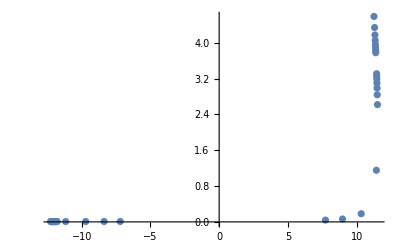

```mathematica
xyzs=Data⟦1⟧;
Length[xyzs]
ListPlot[Data⟦1,All,{1,3}⟧]
```

### What does a periodic orbit (with winding number 1) look like on the section?

A periodic orbit (with winding number 1) looks like a single dot on the section.